# Homework 11

Name: Muhammad Salah Shatla

ID: 201500059

## Problem 1

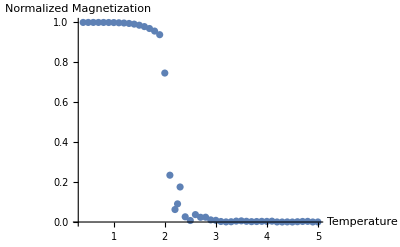

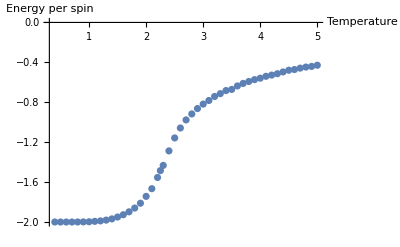

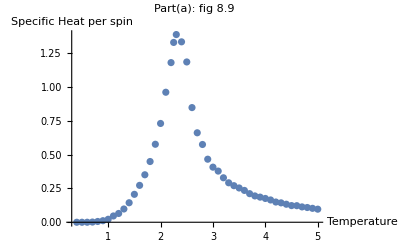

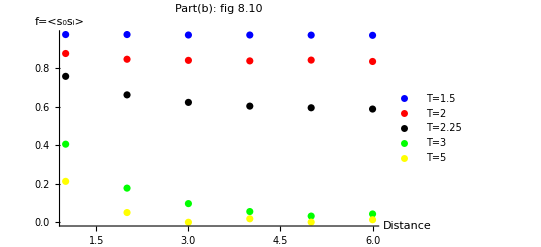

session time = 654.666209

```mathematica
t=SessionTime[];
(* Initializations *)
nMax = 12; (* Lattice dimension *)  nTot = nMax^2;  (* Total number of spins *)
time =10000; (* Number of Monte Carlo repititions *)  
nCut = 1000; 
mag = Table[0.0,{i,time}]; 
totEn = mag; (* Total energy *) 


f=mag; 
For[ii=1,ii≤time,ii++,
f[[ii]]=Table[0,{i,Ceiling[nMax/2]}] 
];
dT=0.1;
temp = Range[0.4,5.0,dT]; (* Temperature range *)
AppendTo[temp,2.25];
magAve = Table[0.0,{i,Length[temp]}]; (* Average magnetization for each temperature *)
EnAve = magAve; (* Average system energy at each temperature *)
hCAve = magAve; (* Average heat capacity at each temperature *)
movie =  magAve; (* movie[[i]] contains all microstates for a given temperature *)
flist= magAve; (*a list with the length of temperature*)
For[ii=1,ii≤Length[temp],ii++,
flist[[ii]]=Table[0,{i,Ceiling[nMax/2]}] (*the magnetic correlation list*)
];

(* spin site matrix: spins are labled from 1 up to nTot  *)
sitMat = Array[0 &,{nMax + 2, nMax + 2}] ;(* Site Matrix; assigns number from 1 to nTot to the sites. *)
sitMat//MatrixForm;
sites = Table[j + (i -1) nMax, {i,nMax},{j,nMax}];
sites//MatrixForm;
sitMat[[2;;nMax+1,2;;nMax+1]] = sites;
sitMat//MatrixForm;

(* making the neighbors at the boundaries *)
sitMat[[1]] = sitMat[[nMax+1]];
sitMat[[All,1]] = sitMat[[All,nMax+1]];
sitMat[[nMax+2]] = sitMat[[2]];
sitMat[[All,nMax+2]] = sitMat[[All,2]];
sitMat//MatrixForm;

(*table for neighbours*)
nTab = Array[0 &,{nTot,4}]; (*  neighbor table *)
k = 1;
Do[
nTab[[k,1]] = sitMat[[i,j+1]];
nTab[[k,2]] = sitMat[[i+1,j]];
nTab[[k,3]] = sitMat[[i,j-1]];
nTab[[k,4]] = sitMat[[i-1,j]]; k+=1,
{i,2,nMax+1},{j,2,nMax+1}];
nTab//MatrixForm;

lat = ConstantArray[1,nTot]; (* Spins are all up, represented in 1D chain *)
engy =-2.0 nTot ; (* Initial energy for all spin up configuration *)

Monitor[
Do[

(* Transition probabilities using Eflipp = eF = ±8, ±4, 0 *)
Do[p[i] = Exp[-i/temp[[nt]]],{i,-8,8,4}];

Do[

Do[
sNN = Total[lat[[nTab[[i]]]]]; (* Nearest neighbors net spin *)
eF = 2 lat[[i]] sNN; (* Eflipp = eF = ±8, ±4, 0 *)

If[RandomReal[] <= Min[1,p[eF]],{lat[[i]]= -  lat[[i]],engy =engy+eF}] ;

,{i,1,nTot}]; 


mag[[mt]] =Total[lat]; (* Total magnetiztion  *)  
totEn[[mt]] =engy; (* Total energy  *)
For[jj=1,jj≤Ceiling[nMax/2],jj++,
f[[mt,jj]]=lat[[1]]*lat[[1+jj*nMax]]]
, {mt,time}];

magAve[[nt]] =Abs[N[ Mean[mag[[Range[nCut,time]]]]]/nTot]; (* Mean of magnetiztion per spin *)
EnAve[[nt]] = Mean[totEn[[Range[nCut,time]]]]; (* ⟨E⟩ average energy  *)
hCAve[[nt]] =Variance[totEn[[Range[nCut,time]]]]/(nTot*temp[[nt]]^2); (* Mean of specific heat per spin *)

For[jj=1,jj≤Ceiling[nMax/2],jj++,
flist[[nt,jj]]=Abs[Mean[f[[All,jj]]]];
];
,{nt,Length[temp]}]
,ProgressIndicator[nt,{1,Length[temp]+1}]];

tmagAveList = Table[{temp[[i]],magAve[[i]]},{i,Length[temp]}];
thCAveList = Table[{temp[[i]],hCAve[[i]]},{i,Length[temp]}];
tEngAveList = Table[{temp[[i]],EnAve[[i]]/nTot },{i,Length[temp]}];

pmag=ListPlot[tmagAveList,AxesLabel->{"Temperature","Normalized Magnetization"},PlotRange->All]
ListPlot[tEngAveList,AxesLabel->{"Temperature","Energy per spin"},PlotRange->All]
ListPlot[thCAveList,AxesLabel->{"Temperature","Specific Heat per spin"},PlotRange->All,PlotLabel->"Part(a): fig 8.9"]

templist={1.5,2,2.25,3,5}; (*plotted temperatures*)
plotf=0*templist;

For[ii=1,ii≤Length[templist],ii++,
If[templist[[ii]]==2.25,
plotf[[ii]]=Last[flist],
plotf[[ii]]=flist[[Floor[(templist[[ii]]-0.4)/dT]+1]]
]
];
pf=0*plotf;
colorlist={Blue,Red,Black,Green,Yellow};

For[ii=1,ii≤Length[pf],ii++,
positionftable=Table[{l,plotf[[ii,l]]},{l,Ceiling[nMax/2]}];
pf[[ii]]=ListPlot[positionftable,PlotRange->All,PlotStyle->colorlist[[ii]],PlotLegends->PointLegend[{"T="<>ToString[templist[[ii]]]}],PlotLabel->"Part(b): fig 8.10"]
];
Quiet[Show[pf[[i]]/.i->Range[1,Length[templist]],PlotRange->All,AxesLabel->{"Distance","f="<>"<s_0s_i>"},AxesOrigin->{0,0}]]

Print["session time = ",SessionTime[]-t]
```

## Part C

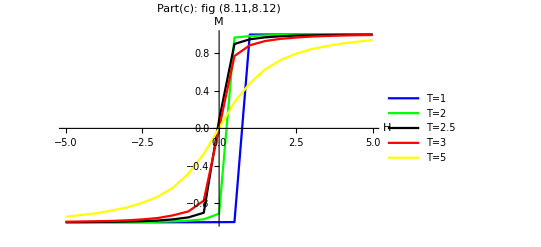

session time = 180.767346

```mathematica
ClearAll["Global`*"]

t=SessionTime[];
(* Initializations *)
nMax = 12; (* Lattice dimension *)  nTot = nMax^2;  (* Total number of spins *)
time =1000; (* Number of Monte Carlo repititions *)  
nCut = 100; (* Assuming that equilibrium is reached after nCut Monte Carlo steps. We cut them. We average from step nCut + 1 up to time *) 

mag = Table[0.0,{i,time}]; (* Magnetization for each MC run *)

temp = {1,2,2.5,3,5}; (* Temperature range *)
h=Range[-5,5,0.5];
magAve = Table[0.0,{i,Length[temp]}]; (* Average magnetization for each temperature *)
For[i=1,i≤Length[temp],i++,
magAve[[i]]=Table[0.0,{j,Length[h]}] (*Average magnetization for every value of H and T*)
]

(* spin site matrix: spins are labled from 1 up to nTot  *)

sitMat = Array[0 &,{nMax + 2, nMax + 2}] ;(* Site Matrix; assigns number from 1 to nTot to the sites. *)
sitMat//MatrixForm;
sites = Table[j + (i -1) nMax, {i,nMax},{j,nMax}];
sites//MatrixForm;
sitMat[[2;;nMax+1,2;;nMax+1]] = sites;
sitMat//MatrixForm;

(* setting the neighbors at the boundaries *)
sitMat[[1]] = sitMat[[nMax+1]];
sitMat[[All,1]] = sitMat[[All,nMax+1]];
sitMat[[nMax+2]] = sitMat[[2]];
sitMat[[All,nMax+2]] = sitMat[[All,2]];
sitMat//MatrixForm;

(*  neighbors table *)
nTab = Array[0 &,{nTot,4}]; (*  neighbor table *)
k = 1;
Do[
nTab[[k,1]] = sitMat[[i,j+1]];
nTab[[k,2]] = sitMat[[i+1,j]];
nTab[[k,3]] = sitMat[[i,j-1]];
nTab[[k,4]] = sitMat[[i-1,j]]; k+=1,
{i,2,nMax+1},{j,2,nMax+1}];
nTab//MatrixForm;

lat = ConstantArray[1,nTot]; (* Spins are all up, represented in 1D chain *)

Monitor[
Do[(* Over temperature *) 


(* Transition probabilities using Eflipp = eF *)
p[x_]:= Exp[-x/temp[[nt]]];

Do[(*over H*)

Do[(* Over Monte Carlo times *)

Do[(* Over spins *) 
sNN = Total[lat[[nTab[[i]]]]]; (* Nearest neighbors net spin *)
eF = 2 lat[[i]] (sNN+h[[ht]]); (* Eflipp = eF*)

If[RandomReal[] <= Min[1,p[eF]],lat[[i]]= -  lat[[i]]] ;

,{i,1,nTot}]; 

mag[[mt]] =Total[lat]; (* Total magnetiztion  *)  

, {mt,time}]; 

magAve[[nt,ht]] =N[ Mean[mag[[Range[nCut,time]]]]]/nTot; (* Mean of magnetiztion per spin *)
,{ht,Length[h]}];
,{nt,Length[temp]}]
,ProgressIndicator[nt,{1,Length[temp]+1}]];
magAve=magAve/Max[magAve];

pmag=0*temp;
colorlist={Blue,Green,Black,Red,Yellow};

For[i=1,i≤Length[temp],i++,
tmagAveList = Table[{h[[j]],magAve[[i,j]]},{j,Length[h]}];
pmag[[i]]=ListLinePlot[tmagAveList,PlotRange->All,PlotStyle->colorlist[[i]],PlotLegends->LineLegend[{"T="<>ToString[temp[[i]]]}]]

]

Quiet[Show[pmag[[i]]/.i->Range[1,Length[temp]],PlotRange->All,PlotLabel->"Part(c): fig (8.11,8.12)",AxesLabel->{"H","M"},AxesOrigin->{0,0}]]

Print["session time = ",SessionTime[]-t]
```

## Part d

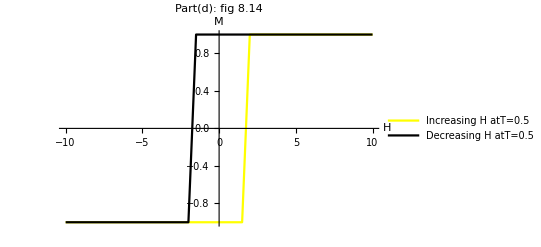

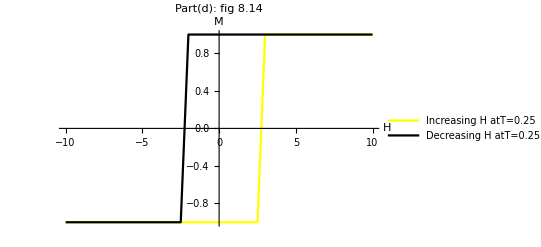

session time = 56.005448

```mathematica
ClearAll["Global`*"]

t=SessionTime[];
(* Initializations *)
nMax = 12; (* Lattice dimension *)  nTot = nMax^2;  (* Total number of spins *)
time =200; (* Number of Monte Carlo repititions *)  
nCut = 100; (* Assuming that equilibrium is reached after nCut Monte Carlo steps. We cut them. We average from step nCut + 1 up to time *) 

mag = Table[0.0,{i,time}]; (* Magnetization for each MC run *)

temp = {0.5,0.25}; (* Temperature range *)
temporarylist=Table[temp[[Ceiling[i/2]]],{i,2*Length[temp]}];
temp=temporarylist; (*to count each temperature twice*)


h=Range[-10,10,0.5];
magAve = Table[0.0,{i,Length[temp]}]; (* Average magnetization for each temperature *)
For[i=1,i≤Length[temp],i++,
magAve[[i]]=Table[0.0,{j,Length[h]}] (*Average magnetization for every value of H and T*)
]

(* spin site matrix: spins are labled from 1 up to nTot  *)

sitMat = Array[0 &,{nMax + 2, nMax + 2}] ;(* Site Matrix; assigns number from 1 to nTot to the sites. *)
sitMat//MatrixForm;
sites = Table[j + (i -1) nMax, {i,nMax},{j,nMax}];
sites//MatrixForm;
sitMat[[2;;nMax+1,2;;nMax+1]] = sites;
sitMat//MatrixForm;

(* setting the neighbors at the boundaries *)
sitMat[[1]] = sitMat[[nMax+1]];
sitMat[[All,1]] = sitMat[[All,nMax+1]];
sitMat[[nMax+2]] = sitMat[[2]];
sitMat[[All,nMax+2]] = sitMat[[All,2]];
sitMat//MatrixForm;

(*  neighbors table *)
nTab = Array[0 &,{nTot,4}]; (*  neighbor table *)
k = 1;
Do[
nTab[[k,1]] = sitMat[[i,j+1]];
nTab[[k,2]] = sitMat[[i+1,j]];
nTab[[k,3]] = sitMat[[i,j-1]];
nTab[[k,4]] = sitMat[[i-1,j]]; k+=1,
{i,2,nMax+1},{j,2,nMax+1}];
nTab//MatrixForm;

lat = ConstantArray[1,nTot]; (* Spins are all up, represented in 1D chain *)

Monitor[
Do[(* Over temperature *) 
If[QuotientRemainder[nt,2][[2]]==0,h=Reverse[h]]; (*we take H decreasing*)
(* Transition probabilities using Eflipp = eF *)
p[x_]:= Exp[-x/temp[[nt]]];

Do[(*over H*)

Do[(* Over Monte Carlo times *)

Do[(* Over spins *) 
sNN = Total[lat[[nTab[[i]]]]]; (* Nearest neighbors net spin *)
eF = 2 lat[[i]] (sNN+h[[ht]]); (* Eflipp = eF*)

If[RandomReal[] <= Min[1,p[eF]],lat[[i]]= -  lat[[i]]] ;

,{i,1,nTot}]; 

mag[[mt]] =Total[lat]; (* Total magnetiztion  *)  

, {mt,time}]; 

magAve[[nt,ht]] =N[ Mean[mag[[Range[nCut,time]]]]]/nTot; (* Mean of magnetiztion per spin *)
,{ht,Length[h]}];
If[QuotientRemainder[nt,2][[2]]==0,h=Reverse[h]] (*putting h in its original form*)
,{nt,Length[temp]}]
,ProgressIndicator[nt,{1,Length[temp]+1}]];
magAve=magAve/Max[magAve];

pmag=0*temp;
colorlist={Yellow,Black,Green,Blue};

For[i=1,i≤Length[temp],i++,
If[QuotientRemainder[i,2][[2]]==1 (*means h increases*),tmagAveList = Table[{h[[j]],magAve[[i,j]]},{j,Length[h]}];
pmag[[i]]=ListLinePlot[tmagAveList,PlotRange->All,PlotStyle->colorlist[[1]],PlotLegends->LineLegend[{"Increasing H at"<>"T="<>ToString[temp[[i]]]}]],
tmagAveList = Table[{h[[Length[h]+1-j]],magAve[[i,j]]},{j,Length[h]}];
pmag[[i]]=ListLinePlot[tmagAveList,PlotRange->All,PlotStyle->colorlist[[2]],PlotLegends->LineLegend[{"Decreasing H at"<>"T="<>ToString[temp[[i]]]}]]]

]
Quiet[Show[pmag[[i]]/.i->{1,2},PlotRange->All,PlotLabel->"Part(d): fig 8.14",AxesLabel->{"H","M"},AxesOrigin->{0,0}]]
Quiet[Show[pmag[[i]]/.i->{3,4},PlotRange->All,PlotLabel->"Part(d): fig 8.14",AxesLabel->{"H","M"},AxesOrigin->{0,0}]]

Print["session time = ",SessionTime[]-t]
```

## Part e&f

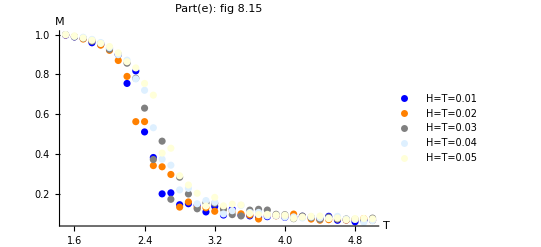

session time = 198.237326

```mathematica
ClearAll["Global`*"]

st=SessionTime[];
(* Initializations *)
nMax = 20; (* Lattice dimension *)  nTot = nMax^2;  (* Total number of spins *)
time =200; (* Number of Monte Carlo repititions *)  
nCut = 100; (* Assuming that equilibrium is reached after nCut Monte Carlo steps. We cut them. We average from step nCut + 1 up to time *) 

mag = Table[0.0,{i,time}]; (* Magnetization for each MC run *)

temp = Range[1.5,5,0.1]; (* Temperature range *)

h=Range[0.01,0.05,0.01];
magAve = Table[0.0,{i,Length[temp]}]; (* Average magnetization for each temperature *)
For[i=1,i≤Length[temp],i++,
magAve[[i]]=Table[0.0,{j,Length[h]}] (*Average magnetization for every value of H and T*)
]

(* spin site matrix: spins are labled from 1 up to nTot  *)

sitMat = Array[0 &,{nMax + 2, nMax + 2}] ;(* Site Matrix; assigns number from 1 to nTot to the sites. *)
sitMat//MatrixForm;
sites = Table[j + (i -1) nMax, {i,nMax},{j,nMax}];
sites//MatrixForm;
sitMat[[2;;nMax+1,2;;nMax+1]] = sites;
sitMat//MatrixForm;

(* setting the neighbors at the boundaries *)
sitMat[[1]] = sitMat[[nMax+1]];
sitMat[[All,1]] = sitMat[[All,nMax+1]];
sitMat[[nMax+2]] = sitMat[[2]];
sitMat[[All,nMax+2]] = sitMat[[All,2]];
sitMat//MatrixForm;

(*  neighbors table *)
nTab = Array[0 &,{nTot,4}]; (*  neighbor table *)
k = 1;
Do[
nTab[[k,1]] = sitMat[[i,j+1]];
nTab[[k,2]] = sitMat[[i+1,j]];
nTab[[k,3]] = sitMat[[i,j-1]];
nTab[[k,4]] = sitMat[[i-1,j]]; k+=1,
{i,2,nMax+1},{j,2,nMax+1}];
nTab//MatrixForm;
spinMat = Array[0 &,{nMax , nMax }];  (* to plot spins as black and white *)
spinMatList = Array[0 &,time]; (* to save spinMat in a list *)

lat = ConstantArray[1,nTot]; (* Spins are all up, represented in 1D chain *)

Monitor[
Do[(*over H*) 

(* Transition probabilities using Eflipp = eF *)
p[x_]:= Exp[-x/temp[[nt]]];

Do[(* Over temperature *)

Do[(* Over Monte Carlo times *)

Do[(* Over spins *) 
sNN = Total[lat[[nTab[[i]]]]]; (* Nearest neighbors net spin *)
eF = 2 lat[[i]] (sNN+h[[ht]]); (* Eflipp = eF*)

If[RandomReal[] <= Min[1,p[eF]],lat[[i]]= -  lat[[i]]] ;

,{i,1,nTot}]; 

Do[  (* Matrix of spins: converting lat into a matrix  *)
spinMat[[i]] = lat[[1+ (i-1)nMax;;i nMax]],{i,nMax}];

spinMatList[[mt]] = spinMat;
mag[[mt]] =Abs[Total[lat]]; (* Total magnetiztion  *)  

, {mt,time}]; 

magAve[[nt,ht]] =N[ Mean[mag[[Range[nCut,time]]]]]/nTot; (* Mean of magnetiztion per spin *)

,{nt,Length[temp]}];
,{ht,Length[h]}]
,ProgressIndicator[ht,{1,Length[h]+1}]];
magAve=magAve/Max[magAve];
pmag=0*h;
colorlist={Blue,Orange,Gray,LightBlue,LightYellow,Pink,Green,Red,Yellow,LightGreen,LightGray,Black,Brown};

For[i=1,i≤Length[h],i++,
tmagAveList = Table[{temp[[j]],magAve[[j,i]]},{j,Length[temp]}];
pmag[[i]]=ListPlot[tmagAveList,PlotRange->All,PlotStyle->colorlist[[i]],PlotLegends->PointLegend[{"H="<>"T="<>ToString[h[[i]]]}]]
]

Quiet[Show[pmag[[i]]/.i->Range[1,Length[h]],PlotRange->All,PlotLabel->"Part(e): fig 8.15",AxesLabel->{"T","M"},AxesOrigin->{1.5,0}]]


Print["session time = ",SessionTime[]-st]
```

## Continue part f

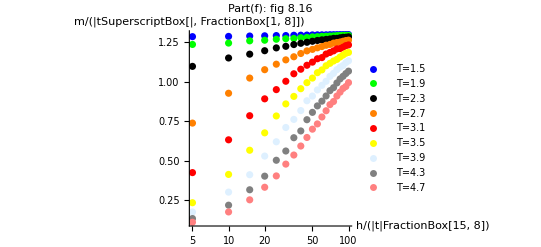

session time = 915.7357191

```mathematica
ClearAll["Global`*"]

st=SessionTime[];
(* Initializations *)
nMax = 20; (* Lattice dimension *)  nTot = nMax^2;  (* Total number of spins *)
time =1000; (* Number of Monte Carlo repititions *)  
nCut = 600; (* Assuming that equilibrium is reached after nCut Monte Carlo steps. We cut them. We average from step nCut + 1 up to time *) 

mag = Table[0.0,{i,time}]; (* Magnetization for each MC run *)

temp = Range[1.5,5,0.4]; (* Temperature range *)

h=Range[0.1,2.0,0.1];
magAve = Table[0.0,{i,Length[temp]}]; (* Average magnetization for each temperature *)
For[i=1,i≤Length[temp],i++,
magAve[[i]]=Table[0.0,{j,Length[h]}] (*Average magnetization for every value of H and T*)
]

(* spin site matrix: spins are labled from 1 up to nTot  *)

sitMat = Array[0 &,{nMax + 2, nMax + 2}] ;(* Site Matrix; assigns number from 1 to nTot to the sites. *)
sitMat//MatrixForm;
sites = Table[j + (i -1) nMax, {i,nMax},{j,nMax}];
sites//MatrixForm;
sitMat[[2;;nMax+1,2;;nMax+1]] = sites;
sitMat//MatrixForm;

(* setting the neighbors at the boundaries *)
sitMat[[1]] = sitMat[[nMax+1]];
sitMat[[All,1]] = sitMat[[All,nMax+1]];
sitMat[[nMax+2]] = sitMat[[2]];
sitMat[[All,nMax+2]] = sitMat[[All,2]];
sitMat//MatrixForm;

(*  neighbors table *)
nTab = Array[0 &,{nTot,4}]; (*  neighbor table *)
k = 1;
Do[
nTab[[k,1]] = sitMat[[i,j+1]];
nTab[[k,2]] = sitMat[[i+1,j]];
nTab[[k,3]] = sitMat[[i,j-1]];
nTab[[k,4]] = sitMat[[i-1,j]]; k+=1,
{i,2,nMax+1},{j,2,nMax+1}];
nTab//MatrixForm;
spinMat = Array[0 &,{nMax , nMax }];  (* to plot spins as black and white *)
spinMatList = Array[0 &,time]; (* to save spinMat in a list *)

lat = ConstantArray[1,nTot]; (* Spins are all up, represented in 1D chain *)

Monitor[
Do[(* Over temperature *) 

(* Transition probabilities using Eflipp = eF *)
p[x_]:= Exp[-x/temp[[nt]]];

Do[(*over H*)

Do[(* Over Monte Carlo times *)

Do[(* Over spins *) 
sNN = Total[lat[[nTab[[i]]]]]; (* Nearest neighbors net spin *)
eF = 2 lat[[i]] (sNN+h[[ht]]); (* Eflipp = eF*)

If[RandomReal[] <= Min[1,p[eF]],lat[[i]]= -  lat[[i]]] ;

,{i,1,nTot}]; 

Do[  (* Matrix of spins: converting lat into a matrix  *)
spinMat[[i]] = lat[[1+ (i-1)nMax;;i nMax]],{i,nMax}];

spinMatList[[mt]] = spinMat;
mag[[mt]] =Abs[Total[lat]]; (* Total magnetiztion  *)  

, {mt,time}]; 

magAve[[nt,ht]] =N[ Mean[mag[[Range[nCut,time]]]]]/nTot; (* Mean of magnetiztion per spin *)

,{nt,Length[temp]}];
,{ht,Length[h]}]
,ProgressIndicator[ht,{1,Length[h]+1}]];
magAve=magAve/Max[magAve];


t=(Max[h]/100)^(8/15); 
h=h/Abs[t]^(15/8);
magAve=magAve/Abs[t]^(1/8);

colorlist={Blue,Green,Black,Orange,Red,Yellow,LightBlue,Gray,Pink,LightGreen,Brown,LightYellow,LightGray};
pmag=0*temp;
For[i=1,i≤Floor[Length[temp]],i++,
tmagAveList = Table[{h[[j]],magAve[[i,j]]},{j,Length[h]}];
pmag[[i]]=ListLogLinearPlot[tmagAveList,PlotRange->All,PlotStyle->colorlist[[i]],PlotLegends->PointLegend[{"T="<>ToString[temp[[i]]]}]]
]

Quiet[Show[pmag[[i]]/.i->Range[1,Length[pmag]],PlotRange->All,PlotLabel->"Part(f): fig 8.16",AxesLabel->{"h/(|t|FractionBox[15, 8])","m/(|tSuperscriptBox[|, FractionBox[1, 8]])"},AxesOrigin->{0,0}]]

Print["session time = ",SessionTime[]-st]
```